```mathematica
Clear["Global`*"]
```

```mathematica
bigbigN=4/3 π(wD/v)^3/(2π/L)^3/L^3
```

wD^3/(6 π^2 v^3)

```mathematica
Cd=(12*π^4)/(5*V)*bigN*kB*(T/thetaD)^3
```

(12 bigN kB π^4 T^3)/(5 thetaD^3 V)

```mathematica
Ce=π^2/(2*V)n*kB*((kB*T)/EF)
```

(kB^2 n π^2 T)/(2 EF V)

```mathematica
Simplify[Solve[Ce==Cd,T]]
```

(T→0
T→-(√(5/6) √kB √n thetaD^(3/2))/(2 √bigN √EF π)
T→(√(5/6) √kB √n thetaD^(3/2))/(2 √bigN √EF π))

```mathematica
((5*343^3)/(24*π^2*(8.16*10^4)))^(1/2)
```

3.23092

```mathematica
(*Question 3*)
```

```mathematica
(1/(23.78*10^-6))*6.022*10^23
(1/(23.78*10^-6))*6.022*10^23*(1/10^10)^3
(3 π^2)^(2/3)*13.6*(0.0253238*0.529^3)^(2/3)
```

2.53238×10^28

0.0253238

3.14111

```mathematica
1/L^3(4*π*k^2)*dk/((2π)/L)^3
```

(dk k^2)/(2 π^2)

```mathematica
1/L^2(2*π*k)*dk/((2*π)/L)^2
```

(dk k)/(2 π)

```mathematica
FullSimplify[(1/2*((2*m)/(hbar^2*e))^(1/2)* √((2*m*e)/hbar^2))/(2 π)]
```

(√(m/(e hbar^2)) √((e m)/hbar^2))/(2 π)

```mathematica
Integrate[c*n/EF*(e/EF)^a,e]
```

(c e (e/EF)^a n)/((1+a) EF)

```mathematica
FullSimplify[Integrate[m/(π*hbar^2)1/(Exp[(e-mu)/(kB*T)]+1),{e,0,∞}]]
```

ConditionalExpression[(kB m T Log[1+ⅇ^(mu/(kB T))])/(hbar^2 π), Re[1/(kB T)]>0]

```mathematica
FullSimplify[Log[Exp[EF]-1]]
```

Log[-1+ⅇ^EF]

5

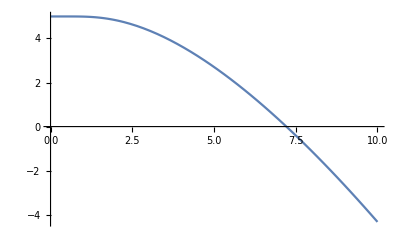

```mathematica
EF=5
Plot[kbt*Log[Exp[EF/kbt]-1],{kbt,0,10}]
```

```mathematica
Limit[Log[x],x->0]
```

-∞